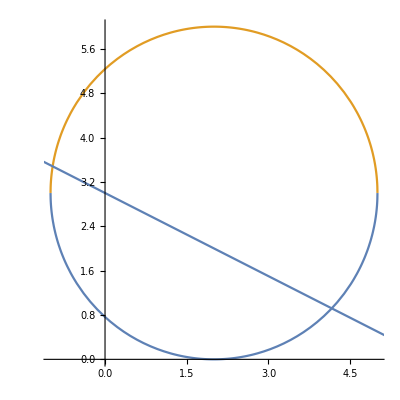

{2/5 (4-√41),1/5 (11+√41)}

{2/5 (4+√41),1/5 (11-√41)}

L'area del Triangolo ABC = (2 √41)/5

L'area del Settore Circolare = ConditionalExpression[9/2 (-π-ArcTan[(-5 √10 (39-√41)^(3/2)+242 √(10 (39-√41)))/(7 √10 (39-√41)^(3/2)-250 √(10 (39-√41)))]+ArcTan[(-5 √10 (39+√41)^(3/2)+242 √(10 (39+√41)))/(7 √10 (39+√41)^(3/2)-250 √(10 (39+√41)))]),C[1]∈ℤ]

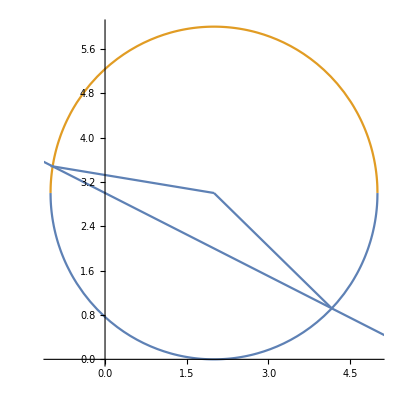

```mathematica
R=3;
centro={2,3};
gamma= (x-centro[[1]])^2 + (y-centro[[2]])^2 == R^2;
retta = y==-1/2 x + 3;


circ=y/.Solve[gamma,y];



g1=Plot[{ circ[[1]], circ[[2]] } ,{x,-1,5} , AspectRatio->1];
g2=Plot[-1/2 x + 3,{x,-10,10}];
Show[g1,g2]
intersez={x,y}/.Solve[ {gamma,retta},{x,y}];
A=intersez[[1]]
B=intersez[[2]]

altezzaT=Abs[1/2 centro[[1]] + 1 centro[[2]] -3]/Sqrt[(1/2)^2 + 1^2];
base=Sqrt[ (A[[1]]- B[[1]])^2 + (A[[2]]- B[[2]])^2];
area=FullSimplify[(base*altezzaT)/2];
Print[" L'area del Triangolo ABC = " , area ]

sost={x->r Cos[th] , y-> r Sin[th]};
retta1= retta /. sost;
gamma1=gamma/.sost;

intersez1={r,th}/.Solve[ {gamma1,retta1},{r,th}];

th1=intersez1[[2,2]];
th2=intersez1[[4,2]];

areaC=Integrate[r , {r,0,3},{th,th1 ,th2 }];

Print[" L'area del Settore Circolare = " , areaC ]

eqac= (y-A[[2]])/(centro[[2]]-A[[2]])==(x-A[[1]])/(centro[[1]]-A[[1]]);
AC=y/.Solve[ eqac,y];

g3=Plot[AC,{x,-1,2}];

eqbc= (y-B[[2]])/(centro[[2]]-B[[2]])==(x-B[[1]])/(centro[[1]]-B[[1]]);
BC=y/.Solve[ eqbc,y];
g4=Plot[BC,{x,2,B[[1]]}];

Show[g1,g2,g3,g4]
```

```mathematica
(*-------------*)
```

2/5 (4-√41)

```mathematica
eqdiff[wf_,wh_]={ y''[t] - af Cos[wf t] + wh^2 y[t]==0 , y'[0]==0,y[0]==0};
sol[wh_,wf_]=y[t]/.DSolve[eqdiff[wf,wh],y[t],t];
```